## Mathematical Analysis Midterm

## April 24, 2021. If you get bogged down on a problem, move on, and come back. No problem is meant to be very long.

## 1. Properties of the Real Numbers (4 pts)

In the following, you can use P1 to P9 freely and without citing which ones you are using. a > b by definition means that  a-b is in P, where P is the set of positive numbers.  P10 to P12 are as follows:
-Graphics-
You job is to show that if a > 1 then a^2>a.

(a) Begin by stating what a>1 by definition means.


That is what you get to assume.

(b) Also state what a^2>a by definition means.


That is what you are trying to prove.

(c) Use P10-P12 to prove (b) from (a). If you need to use it, you can assume 1 is in P without also proving that.

## 2. Induction (3 pts)

You are going to show that this formula is always true, by induction:

```mathematica
∑_(k=1)^n k^2=1/6 n (n+1) (2 n+1)
```

(a) First check that it is true if n=1:



(b) Now show that if you assume it is true for n=l then it is true for n=l+1.

## 3. Domains, Ranges, and Composition of Functions (4 pts)

Spivak defines even and odd functions as follows:

-Graphics-

For two functions f and g, consider the four cases: (i) f even, g even; (ii)  f even, g odd; (iii) f odd, g even; (iv) f odd, g odd.  For each of the four cases, determine whether the composition f∘g is even, odd, or maybe not necessarily either. You may assume that the domain of both functions is all of the real numbers.

For each case, you will be starting off with what (f∘g)(-x) means.

HINT: If you are uncertain what that means, you might need to remind yourself what (f∘g)(x) means.

(i) EVEN EVEN CASE    (f∘g)(-x)=



(ii) EVEN ODD CASE     (f∘g)(-x)=



 (iii) ODD EVEN CASE   (f∘g)(-x)=



(iv) ODD ODD CASE      (f∘g)(-x)=

## 4. Graphs (4 pts)

Let f(x)=mx. Let g(x)=nx. m and n are any numbers, but Spivak draws a graph where m is positive and n is negative as an example:
-Graphics-
The graph is showing that (0, 0) is where the two lines meet, that (1, m) is a point on the graph of f(x), and that (1, n) is a point on the graph of g(x).

Clearly, the vertical line has length |m-n|.

(a) What is the length of each of the two sloped lines?




(b) You now have the lengths of each of three sides of a triangle. Write down the condition (but do not solve it) that the triangle is a right triangle (e.g., write down what the Pythagorean theorem says if this triangle is a right triangle).




(c) Now solve the condition you found in part (b) to get a pleasantly simple equation involving m and n. Joyfully, you have derived the condition that two lines are perpendicular!

## 5. The Limits Poem (2 pts)

Definition: we say that f(x) has a limit of l at a and write

```mathematica
f(x)=lxa
```

if and only if

(a) For any ϵ>0 there exists a δ > 0 such that if |x-a|<δ then |f(x)-l|<ϵ.
(b) For any ϵ>0 there exists a δ > 0 such that if 0<|x-a|<δ then |f(x)-l|<ϵ.
(c) For any ϵ>0 there exists a δ > 0 such that if |x-a|<δ then 0<|f(x)-l|<ϵ.
(d) For any ϵ>0 there exists a δ > 0 such that if 0<|x-a|<δ then 0<|f(x)-l|<ϵ.

Cross out the three wrong definitions.

## 6. Limit of 1/x^2at a=1 with l=1 (5 pts)

The problem is to find a δ > 0 such that |1/x^2-1|<ϵ.

You have done a lot of problems like these. You can skip over the graph and the two hints if reading my hints just slows you down.

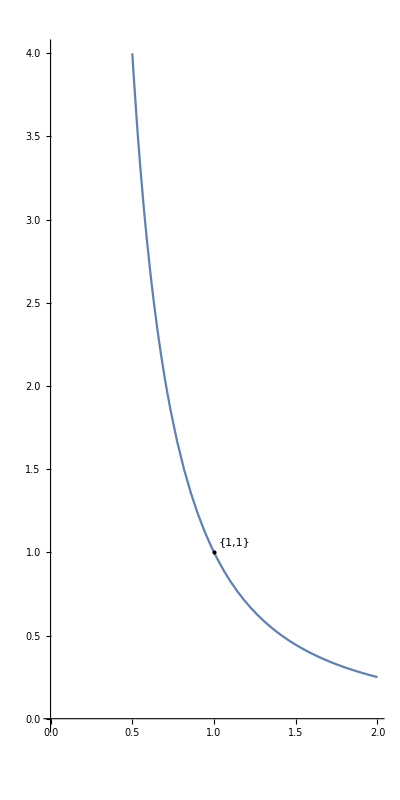

```mathematica
With[{pt={1,1}}, Plot[1/x^2,{x,0,2}, PlotRange->{{0, 2}, {0, 4}}, AspectRatio->2, {Epilog->{PointSize[Large],Point[pt],Text[pt,Offset[{20,10},pt]]}}]]
```

HINT 1: Start off by re-writing |1/x^2-1| as (|x+1||x-1|)/(|x^2|).
HINT 2: You now have three factors. Next get bounds on the factors of |x+1| and 1/(|x^2|) by demanding  |x-1|<1/2. So this is going to be one of those problems where in the end δ is the min of 1/2 and something else involving ϵ.

The whole next page is blank so that you have space to work.

## Space to Do Problem 6

## A Sanity Check for Problem 6

Check your formula for δ, by evaluating it with ϵ = 2. What is δ? Is 1/x^2 within ϵ of 1 if x is within δ of 1?

## 7. A Proof Requiring Little More than the Definition of the Limit (3 pts)

Prove that if the limit as x→a of f(x) exists and is l, then it is also true that the limit as x→2a of f(x/2) exists and is l.

To do this proof, the very first thing you do is write the definition of the limit out for the above two limits. Since the deltas in the two statements are not going to be the same, in the second statement call it δ' instead. The job is essentially to find the relationship between δ and δ' that makes the two statements equivalent.